# Three-State Markov Chain Model

## Mathematica functions for simulation of discrete hidden Markov chains

## GW 2025

## Three-state Markov Chain Construction

```mathematica
CellPrint[TextCell["Reaction Scheme",CellTags->"Scheme","Subsection"]]
```

### Reaction Scheme

We consider a three-state model with the following connectivity and transition probabilities: 
  -Graphics-

```mathematica
Grid[{{"  to state →\rfrom state\r     ↓","S_1","S_2","S_3"},
{"S_1","p(k_11)=1-(p(k_12)+p(k_13))","p(k_12)=1-ⅇ^(-SubscriptBox[k, 12])","p(k_13)=1-ⅇ^(-SubscriptBox[k, 13])"},
{"S_2","p(k_21)=1-ⅇ^(-SubscriptBox[k, 21])","p(k_22)=1-(p(k_21)+p(k_23))","p(k_23)=1-ⅇ^(-SubscriptBox[k, 23])"},
{"S_3","p(k_31)=1-ⅇ^(-SubscriptBox[k, 31])","p(k_32)=1-ⅇ^(-SubscriptBox[k, 32])","p(k_33)=1-(p(k_31)+p(k_32)"}},Frame->All]
```

to state →\rfrom state\r     ↓ | S_1 | S_2 | S_3
S_1 | p(k_11)=1-(p(k_12)+p(k_13)) | p(k_12)=1-ⅇ^(-SubscriptBox[k, 12]) | p(k_13)=1-ⅇ^(-SubscriptBox[k, 13])
S_2 | p(k_21)=1-ⅇ^(-SubscriptBox[k, 21]) | p(k_22)=1-(p(k_21)+p(k_23)) | p(k_23)=1-ⅇ^(-SubscriptBox[k, 23])
S_3 | p(k_31)=1-ⅇ^(-SubscriptBox[k, 31]) | p(k_32)=1-ⅇ^(-SubscriptBox[k, 32]) | p(k_33)=1-(p(k_31)+p(k_32)

```mathematica
Unset[{p11,p12,p13,p21,p22,p23,p31,p32,p33}]  (* In case we want to reset Subscript[p, ij] *)
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
CellPrint[TextCell["Set Parameters",CellTags->"params","Subsection"]]
```

### Set Parameters

We defined for our example: k12 = 5 s^-1, k21 = 0.5 s^-1, k23 = 1. s^-1, k32 = 0.1 s^-1. k13 and k31 were 0. The fastest rate is 5 s^-1 ⟷ 0.2 s transition time, hence the sampling frequency should be at least 10 s^-1 = 10 Hz.

```mathematica
k12=6.;k21=0.5;k23=1.;k32=0.5;k13=0;k31=0;
```

```mathematica
δ=10.;
```

The probabilities to observe a transition i → j in the time interval 1/δ is

```mathematica
p12=1-ⅇ^(-k12/δ);
p13=1-ⅇ^(-k13/δ);
p21=1-ⅇ^(-k21/δ);
p23=1-ⅇ^(-k23/δ);
p31=1-ⅇ^(-k31/δ);
p32=1-ⅇ^(-k32/δ);
```

If there is no transition observed, th state stays the same, i.e. the remaining probatility to one is:

```mathematica
p11=1-(p12 + p13) ;
p22= 1-(p21 + p23) ;
p33= 1-(p31 + p32) ;
```

```mathematica
tm3state={{p11,p12,p13},{p21,p22,p23},{p31,p32,p33}}
```

{{0.548812,0.451188,0.},{0.0487706,0.856067,0.0951626},{0.,0.0487706,0.951229}}

```mathematica
MatrixForm[tm3state]
```

(0.548812 | 0.451188 | 0.
0.0487706 | 0.856067 | 0.0951626
0. | 0.0487706 | 0.951229)

```mathematica
CellPrint[TextCell["Generate noisy data",CellTags->"data","Subsection"]]
```

### Generate noisy data

Generate data that is superimposed by noise that follows a Gaussian distribution (NormalDistribution[mean,width]):

```mathematica
hmp=HiddenMarkovProcess[{0.5,0.3,0.2},tm3state,
{NormalDistribution[1.,0.15],NormalDistribution[2.,0.35],NormalDistribution[3.,0.25]}(*{ExponentialDistribution[1],ExponentialDistribution[1.5],ExponentialDistribution[3]}*)(*{{0.25,0.65,0.1},{0.4,0.3,0.3},{0.35,0.1,0.55}}*)]
```

HiddenMarkovProcess[{0.5,0.3,0.2},{{0.548812,0.451188,0.},{0.0487706,0.856067,0.0951626},{0.,0.0487706,0.951229}},{NormalDistribution[1.,0.15],NormalDistribution[2.,0.35],NormalDistribution[3.,0.25]}]

Use the data to generate a time sequence of length 1000 that contains random noise:

```mathematica
observed=RandomFunction[hmp,{0,1000}]
```

TemporalData[…]

... and look at it:

```mathematica
Manipulate[ListPlot[observed,
Joined->join,GridLines->{None,{1,2,3}},
PlotLabel->"three-state HMM",LabelStyle->Directive[fs, Black],
PlotStyle->{color,Thickness[thn]},
(*Axes->{True,False},*)
Ticks->{Automatic,{1,2,3}},
AxesLabel->{"observation \rframes","observed\rsignal"},
AspectRatio->1/3,ImageSize-> is],
{color,{Blue,RGBColor[0.5,0.5,0.85],Black,Darker[Gray],Orange,Red,Darker[Green]}},
{{fs,21,"font size"},{14,18,21,24,28}},
{{join,False,"join points"},{True,False}},
{{thn,0.005,"line thickness"},0.001,0.025},
{{is,720,"image size"},{450,650,720,950,1080}}]
```

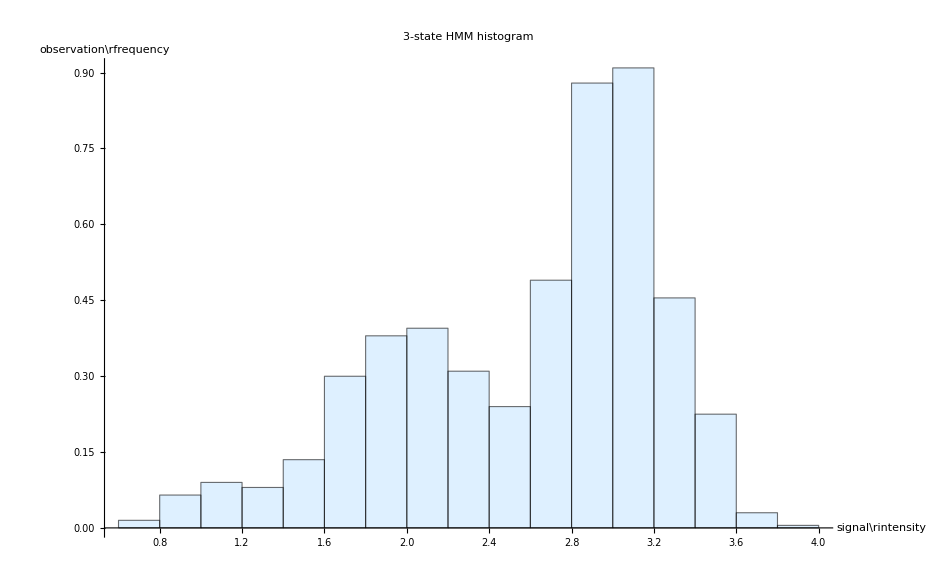

```mathematica
Histogram[observed,Automatic,"PDF",ChartStyle->{LightBlue},PlotLabel->"3-state HMM histogram",LabelStyle->Directive[21, Black],AxesLabel->{"signal\rintensity","observation\rfrequency"},ImageSize-> 950]
```

```mathematica
Button["Enter new rates",NotebookLocate[{"MathCode_21_HiddenMM-3state.nb","params"}],Background->LightYellow]
```

Enter new rates

```mathematica
Button["Generate new trace",NotebookLocate[{"MathCode_21_HiddenMM-3state.nb","data"}],Background->LightYellow]
```

Generate new trace

```mathematica
CellPrint[TextCell["Markov Process Reconstruction",CellTags->"HMMreconstruction","Subsection"]]
```

### Markov Process Reconstruction

Now, try to reconstruct the underlying parameters (inital values, transistion matrix, emission probabilities):

```mathematica
class=HiddenMarkovProcess[3,(*PoissonDistribution[μ]*)(*ExponentialDistribution[λ]*)NormalDistribution[xBar,sd]];
```

Try with your own initial guess:

```mathematica
startValueHMM=HiddenMarkovProcess[{1/4,1/4,1/2},{{0.25,0.7,0.05},{0.4,0.3,0.3},{0.05,0.4,0.55}},{ExponentialDistribution[2],ExponentialDistribution[2],ExponentialDistribution[3]}]
```

HiddenMarkovProcess[{1/4,1/4,1/2},{{0.25,0.7,0.05},{0.4,0.3,0.3},{0.05,0.4,0.55}},{ExponentialDistribution[2],ExponentialDistribution[2],ExponentialDistribution[3]}]

```mathematica
EstimatedProcess[observed,class,startValueHMM]
```

HiddenMarkovProcess[{0.,0.,1.},{{0.402441,0.596999,0.000560371},{0.420572,0.469108,0.11032},{0.0637868,0.0071159,0.929097}},{NormalDistribution[3.0952,0.201316],NormalDistribution[2.96164,0.259445],NormalDistribution[1.88793,0.446649]}]

... or let the Baum-Welch algorithm work for you:

```mathematica
EstimatedProcess[observed,class,(*ProcessEstimator->"ViterbiTraining"*)ProcessEstimator->"BaumWelch"]
```

HiddenMarkovProcess[{1.,3.36952×10^-174,5.78346×10^-30},{{0.575834,0.0167042,0.407462},{3.99451×10^-22,0.936058,0.0639423},{0.0521918,0.0856498,0.862158}},{NormalDistribution[1.04627,0.141471],NormalDistribution[3.02324,0.242335],NormalDistribution[1.98516,0.335211]}]

Transistion matrix:

```mathematica
MatrixForm[{{0.5990316495068696,1.453491501246884*^-22,0.4009683504931303},{3.747479792624302*^-8,0.9577935121782312,0.0422064503469711},{0.04466271334282012,0.0689868011313507,0.8863504855258291}}]
```

(0.599032 | 1.45349×10^-22 | 0.400968
3.74748×10^-8 | 0.957794 | 0.0422065
0.0446627 | 0.0689868 | 0.88635)

Noise calculated from the emission probability matrix:

```mathematica
TableForm[{NormalDistribution[0.9698485603153368,0.10880303080769445],NormalDistribution[2.9904399825787706,0.2616666564053952],NormalDistribution[2.0188959382099747,0.3779108808771689]}]
```

NormalDistribution[0.969849,0.108803]
NormalDistribution[2.99044,0.261667]
NormalDistribution[2.0189,0.377911]

The result is amazingly close to the simulation input!

With noise:

```mathematica
proc=HiddenMarkovProcess[{0.5,0.3,0.2},tm3state,{NormalDistribution[1.,0.15],NormalDistribution[2.,0.35],NormalDistribution[3.,0.25]}]
```

HiddenMarkovProcess[{0.5,0.3,0.2},{{0.606531,0.393469,0.},{0.0487706,0.856067,0.0951626},{0.,0.0487706,0.951229}},{NormalDistribution[1.,0.15],NormalDistribution[2.,0.35],NormalDistribution[3.,0.25]}]

```mathematica
data=RandomFunction[proc,{0,100},100]
```

TemporalData[…]

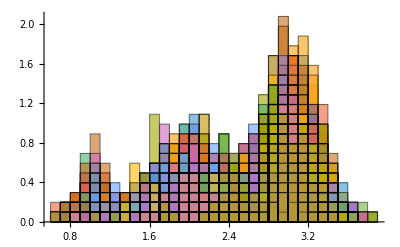

```mathematica
Histogram[data,Automatic,"PDF"]
```

```mathematica
EstimatedProcess[(*observed*)data,HiddenMarkovProcess[3,"Gaussian"]]
```

HiddenMarkovProcess[{0.461639,0.191129,0.347232},{{0.57398,4.28941×10^-7,0.426019},{0.000171679,0.953472,0.0463563},{0.0473265,0.0988215,0.853852}},{NormalDistribution[0.997804,0.138286],NormalDistribution[3.00114,0.25231],NormalDistribution[2.00119,0.348876]}]

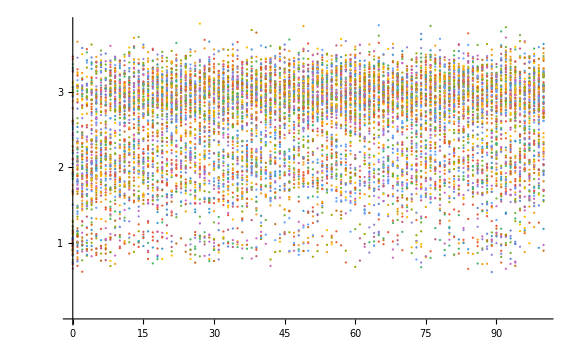

```mathematica
ListPlot[(*observed*)data,(*Filling->Axis,*)Ticks->{Automatic,{1,2,3}},ImageSize->Large]
```

```mathematica
Graph[hmp,ImageSize->450]
```

Graph[HiddenMarkovProcess[{0.5,0.3,0.2},{{0.606531,0.393469,0.},{0.0487706,0.856067,0.0951626},{0.,0.0487706,0.951229}},{NormalDistribution[1.,0.15],NormalDistribution[2.,0.35],NormalDistribution[3.,0.25]}],ImageSize→450]

## Simulation of the Time Series

```mathematica
dmp=DiscreteMarkovProcess[1,tm3state]
```

DiscreteMarkovProcess[1,{{0.606531,0.393469,0.},{0.0487706,0.856067,0.0951626},{0.,0.0487706,0.951229}}]

```mathematica
hmmTimeSeries=RandomFunction[dmp,{0,500}]
```

TemporalData[…]

```mathematica
Manipulate[ListPlot[hmmTimeSeries,
Joined->join,GridLines->{None,{1,2,3}},
PlotLabel->"three-state HMM",LabelStyle->Directive[fs, Black],
PlotStyle->{color,Thickness[thn]},
(*Axes->{True,False},*)
Ticks->{Automatic,{1,2,3}},
AxesLabel->{"observation \rframes","state"},
AspectRatio->1/3,ImageSize-> is],
{color,{Blue,RGBColor[0.5,0.5,0.85],Black,Darker[Gray],Orange,Red,Darker[Green]}},
{{fs,21,"font size"},{14,18,21,24,28}},
{{join,False,"join points"},{True,False}},
{{thn,0.005,"line thickness"},0.001,0.025},
{{is,720,"image size"},{450,650,720,950,1080}}]
```

## Statistics of State Population

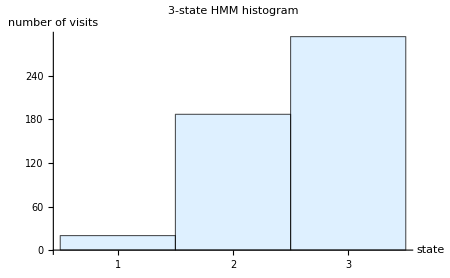

```mathematica
Histogram[hmmTimeSeries,ChartStyle->{LightBlue},PlotLabel->"3-state HMM histogram",LabelStyle->Directive[21, Black],(*AxesLabel->"number of visits"*)AxesLabel->{"state","number of visits"},Ticks->{{1,2,3},Automatic},ImageSize-> 450]
```